## Week 7 - Lecture 7: Importance Sampling in Monte Carlo Method

Resources  --  Video  &  Notes 7g

A method for faster convergence than sampling from an uniform distribution. Check page 2.

Essentially, Integration is nothing but a continuous sum. By Monte Carlo sampling from uniform distribution, we may be wasting time on samples that doesn't help much; importance sampling helps in considering only those random samples which contribute the most weightage towards the solution. Essentially, we can choose a probability distribution p(x) that mimics f(x) in a rough way, meaning wherever f(x) is larger, p(x) also needs to be larger & so on.

Note:  If the p(x) = 1/(b-a), what we essentially have is the uniform distribution (for naive Monte Carlo Integration)

#### Estimating π

Consider this function from prev. lecture. It keeps falling down as x increases.

```mathematica
f[x_] = 4/(1+x^2) 
actualsol=Integrate[f[x], {x,0,1}]
```

4/(1+x^2)

π

Let us model it with a similar exponentially decaying function. p(x) = A Exp[-x]

Let us normalize p(x) for the definite integral to make things simple (so that we can actually treat p(x) as a probability distribution).
That is, we want ∫p(x)dx == 1 in limits (0,1). Substituting p(x) and solving for A, we have p(x) as follows:

```mathematica
A=1/Integrate[Exp[-x], {x,0,1}] (*Gives A*)
```

ⅇ/(-1+ⅇ)

```mathematica
p[x_] = A Exp[-x]  (*Normalized p(x)*)
```

ⅇ^(1-x)/(-1+ⅇ)

```mathematica
Integrate[p[x], {x,0,1}] (*Verify if normalized*)
```

1

How do we now sample from this distribution? Ofcourse you can write your own function to sample from a distribution.
But let's do it easily using Mathematica and create a ProbabilityDistribution[] from a function.

```mathematica
Dist = ProbabilityDistribution[p[x], {x,0,1}];
```

Let us first verify if we're on the right track.

```mathematica
PDF[Dist,x]
```

Piecewise[{{ⅇ^(1-x)/(-1+ⅇ), 0<x<1}, {0, True}}]

```mathematica
Plot[PDF[Dist, x], {x,0,1}]
```

-Graphics-

```mathematica
Plot[PDF[Dist, x], {x,-1,2}] (*Verify if zero outside [0,1]*)
```

-Graphics-

```mathematica
RandomVariate[Dist, 10] (*Drawing some random samples*)
```

{0.058932,0.1293,0.70169,0.0459074,0.347684,0.0764342,0.956844,0.348236,0.23989,0.930279}

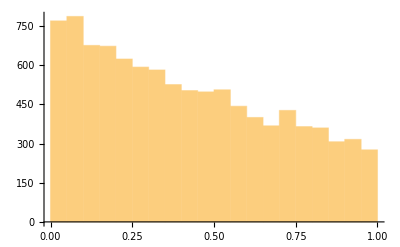

```mathematica
Histogram[RandomVariate[Dist, 10000]]
```

Let us now apply importance-sampling based Monte Carlo Integration to the below target function from our p(x).

```mathematica
targetf[x_] = f[x]/p[x]
```

(4 (-1+ⅇ) ⅇ^(-1+x))/(1+x^2)

```mathematica
Table[targetf[RandomVariate[Dist]], {10}] (*Check if works*)
```

{3.40597,3.0755,2.53033,3.40834,2.72356,2.60195,3.41411,3.43656,2.98802,3.40689}

```mathematica
data = Table[ (*Let's do Monte Carlo now*)
n = 2^k;
estimate = Mean[Table[Mean[Table[targetf[RandomVariate[Dist]], {n}]], {1}]];
{n, estimate}, {k,5,10}];
TableForm[data]
ListPlot[data, Joined->True]
```

32 | 3.19901
64 | 3.18179
128 | 3.13138
256 | 3.1566
512 | 3.14269
1024 | 3.13865

-Graphics-

Homework:
- We have set the number of means to take as 1. (Unlike 1000 in prev. lecture since it takes long time).
   So perform a timing analysis for that as well as different ranges of n (and try plotting a table)
- Perform error analysis like prev. lecture
- Try with a Power law distribution instead of this p(x), or try p(x)=αExp[-βx] or some Exp[-x^2].

In fact, timing vs accuracy actually depends upon the p(x). If rightly chosen, we can perform quick & accurate operations.
This whole thing theoretically is called as Minimization of Variance.
Basically, it means to reduce the error-bars and speed up the convergence.

Homework 2:
- Try the same for the prev. lecture's ln(x) problem